```mathematica
4*m*v/(e*B)
```

48972.2

```mathematica
50000/32.3
```

```mathematica
1547.9876160990714
```

```mathematica
A=.
```

```mathematica
sol=DSolve[{y''[t]==-k^2 y[t],y'[0]==(v+dv)*Sin[dθ/2],y[0]==dw1 Sin[dθ/2]+m*dv/(e*B),x''[t]==0,x[0]==0,x'[0]== vxwf},{y[t],x[t]},t]
```

{{y[t]→1/(B e k)(dv k m Cos[k t]+B dw1 e k Cos[k t] Sin[dθ/2]+B dv e Sin[dθ/2] Sin[k t]+B e v Sin[dθ/2] Sin[k t]),x[t]→t vxwf}}

```mathematica
dtot=100000
dw = 50000
B=1.5*10^-14
v=32.3
E0=-(dtot*B*v)/(dw*4)
e=1.60217646*10^-19
m=9.10938188*10^-31
dw1=dw/2
```

100000

50000

1.5×10^-14

32.3

-2.4225×10^-13

1.60218×10^-19

9.10938×10^-31

25000

```mathematica
β=(e (4 E0^2+B E0 v))/(4 (m v^3))
```

1.53148×10^-19

```mathematica
k=Sqrt[e*vxwf *β/m]
```

0.000164122 √vxwf

```mathematica
vxwf=Sqrt[(v+dv)^2*Cos[dθ/2]^2-e*B*v*dtot*dw1*Sin[dθ/2]/(m*2*dw)]
```

√((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])

```mathematica
ysol[t_]=y[t]/.sol[[1]]
xsol[t_]=x[t]/.sol[[1]]
```

1/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))2.53532×10^36 (1.49505×10^-34 dv Cos[0.000164122 t ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)] ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)+9.86071×10^-33 Cos[0.000164122 t ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)] ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4) Sin[dθ/2]+7.76254×10^-32 Sin[dθ/2] Sin[0.000164122 t ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)]+2.40326×10^-33 dv Sin[dθ/2] Sin[0.000164122 t ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)])

t √((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])

```mathematica
subs={dθ->.001,dv->3.25*10^-4*v/4*{-1,0,1}}
```

{dθ→0.001,dv→{-0.00262438,0.,0.00262438}}

```mathematica
vyf=ysol'[dw/vxwf]/.subs
vxf=vxwf/.subs
ArcTan[vyf/vxf]
```

{-0.00860575,-0.0095252,-0.0104447}

{32.2809,32.2835,32.2861}

{-0.00026659,-0.000295048,-0.000323505}

-0.00026659

{-32.843}

```mathematica
dtot=.
dw =.
B=.
v=.
E0=-(dtot*B*v)/(dw*4)
e=.
m=.
dw1=.
β=.
k=.
vxwf=.
```

-(B dtot v)/(4 dw)

```mathematica
vyf=ysol'[dw/vxwf]
```

0.+1/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))2.53532×10^36 (0.+7.76254×10^-32 Cos[8.20609/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))] (0.+0.000164122 ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)) Sin[dθ/2]+2.40326×10^-33 dv Cos[8.20609/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))] (0.+0.000164122 ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)) Sin[dθ/2]-1.49505×10^-34 dv (0.+0.000164122 ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)) ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4) Sin[8.20609/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))]-9.86071×10^-33 (0.+0.000164122 ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4)) ((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4) Sin[dθ/2] Sin[8.20609/(((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])^(1/4))])

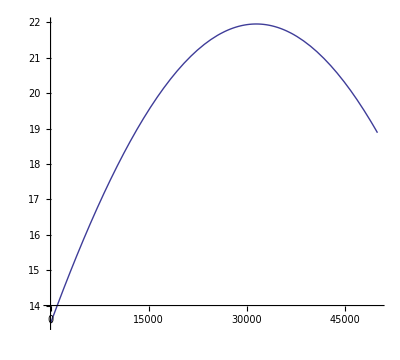

```mathematica
ParametricPlot[{vxwf*t,ysol[t]}/.{dθ->.001,dv->3.25*10^-4*v/4},{t,0,dw/vxf[[2]]},AspectRatio->.9]
```

```mathematica
vxwf*t
```

{32.2809,32.2835,32.2861}

t √((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])

```mathematica
{ysol[t],xsol[t][[2]]}/.{dθ->.001,dv->3.25*10^-4*v/4}
```

{4.46194×10^35 (3.02441×10^-35 Cos[0.000932555 t]+3.88159×10^-35 Sin[0.000932555 t]),32.2861}

```mathematica
vxwf/.subs
```

{32.2809,32.2835,32.2861}

```mathematica
xsol[t]
```

t √((32.3+dv)^2 Cos[dθ/2]^2-2130.37 Sin[dθ/2])

```mathematica
{ysol[t],vxwf*t}/.{dθ->.001,dv->3.25*10^-4*v/4}
```

{4.46194×10^35 (3.02441×10^-35 Cos[0.000932555 t]+3.88159×10^-35 Sin[0.000932555 t]),32.2861 t}

```mathematica
vxwf=Sqrt[(v+dv)^2*Cos[dθ/2]^2-e*B*v*dtot*dw1*Sin[dθ/2]/(m*2*dw)]
```

```mathematica
v Cos[dθ/2] √((dv/v+1)^2 -(B dtot dw1 e Sin[dθ/2])/(Cos[dθ/2]^2 2 dw m v))
```

```mathematica
v Cos[dθ/2]((1+dv/v)-(B dtot dw1 e Sin[dθ/2])/(Cos[dθ/2]^2 4 dw m v))
v (1-dθ^2/8)((1+dv/v)-(B dtot dw1 e Sin[dθ/2])/(Cos[dθ/2]^2 4 dw m v))
```

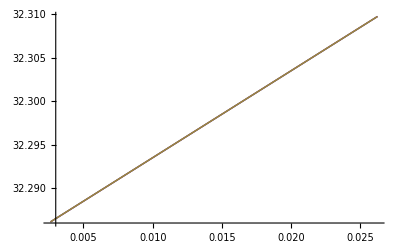

```mathematica
Plot[{32.3 (1-dθ^2/8) (1+0.030959752321981428 dv-1.0209869416321398 Sec[dθ/2] Tan[dθ/2])/.dθ->.001,vxwf/.dθ->.001,(v+dv-(B dtot dw1 e dθ)/(8 dw m))/.dθ->0.001},{dv,3.25*10^-4*v/4,3.25*10^-3*v/4}]
```